```mathematica
Needs["NDSolve`FEM`"];
InCyl[x0_,y0_,z0_,a0_,b0_,c0_,x_,y_,z_,L_,R_]:=(
v0={x0,y0,z0};
hv=v0-(L/2)*{a0,b0,c0};
xv={x,y,z};
dv=xv-hv;
rv={a0,b0,c0};
hv2=hv+L*rv;
dv2=xv-hv2;
proj2=dv2.rv;
proj=dv.rv;
norm=Norm[dv]*Sin[ArcCos[dv.rv/Norm[dv]]];
If[(proj>=0&&proj<=L&&norm<=R)||
(proj≤0&&Norm[dv]≤R)||
(proj2≥0&&Norm[dv2]≤R),1,0]
);
stressOperator[Y_,ν_]:={Inactive[Div][({{0,0,-((Y ν)/((1-2 ν) (1+ν)))},{0,0,0},{-(Y/(2 (1+ν))),0,0}}.Inactive[Grad][w[x,y,z],{x,y,z}]),{x,y,z}]+Inactive[Div][({{0,-((Y ν)/((1-2 ν) (1+ν))),0},{-(Y/(2 (1+ν))),0,0},{0,0,0}}.Inactive[Grad][v[x,y,z],{x,y,z}]),{x,y,z}]+Inactive[Div][({{-((Y (1-ν))/((1-2 ν) (1+ν))),0,0},{0,-(Y/(2 (1+ν))),0},{0,0,-(Y/(2 (1+ν)))}}.Inactive[Grad][u[x,y,z],{x,y,z}]),{x,y,z}],Inactive[Div][({{0,0,0},{0,0,-((Y ν)/((1-2 ν) (1+ν)))},{0,-(Y/(2 (1+ν))),0}}.Inactive[Grad][w[x,y,z],{x,y,z}]),{x,y,z}]+Inactive[Div][({{0,-(Y/(2 (1+ν))),0},{-((Y ν)/((1-2 ν) (1+ν))),0,0},{0,0,0}}.Inactive[Grad][u[x,y,z],{x,y,z}]),{x,y,z}]+Inactive[Div][({{-(Y/(2 (1+ν))),0,0},{0,-((Y (1-ν))/((1-2 ν) (1+ν))),0},{0,0,-(Y/(2 (1+ν)))}}.Inactive[Grad][v[x,y,z],{x,y,z}]),{x,y,z}],Inactive[Div][({{0,0,0},{0,0,-(Y/(2 (1+ν)))},{0,-((Y ν)/((1-2 ν) (1+ν))),0}}.Inactive[Grad][v[x,y,z],{x,y,z}]),{x,y,z}]+Inactive[Div][({{0,0,-(Y/(2 (1+ν)))},{0,0,0},{-((Y ν)/((1-2 ν) (1+ν))),0,0}}.Inactive[Grad][u[x,y,z],{x,y,z}]),{x,y,z}]+Inactive[Div][({{-(Y/(2 (1+ν))),0,0},{0,-(Y/(2 (1+ν))),0},{0,0,-((Y (1-ν))/((1-2 ν) (1+ν)))}}.Inactive[Grad][w[x,y,z],{x,y,z}]),{x,y,z}]};
```

```mathematica
hl={};
Fl={};
For[h=-0.99,h<-0.9,
h=h+0.01;
A=RegionPlot3D[InCyl[0,0,0,Sqrt[2]/2,Sqrt[2]/2,0,x,y,z,1,1]==1,{x,-4,4},{y,-4,4},{z,-4,4},Mesh->None,PlotPoints->100,PlotStyle->Directive[Green,Opacity[0.8]],Boxed->False,BoundaryStyle->None,ImageSize->600,Axes->False,PlotRange->{-4,4}];
mesh=ToElementMesh[DiscretizeGraphics[A],"MeshOrder"->1];
Subscript[Γ,D]={DirichletCondition[{u[x,y,z]==0.,v[x,y,z]==0.,w[x,y,z]==0.},{z≥h}]};
Subscript[Γ2,D]={DirichletCondition[{u[x,y,z]==0.,v[x,y,z]==0.,w[x,y,z]==-z+h},{z<h}]};
E0=10^6;
V0=0;
mf=NDSolveValue[{stressOperator[E0,V0]=={0,0,0},Subscript[Γ,D],Subscript[Γ2,D]},{u,v,w},{x,y,z}∈mesh];
test[mf_,x_,y_,z_]:=(
{mf[[1]][x,y,z],mf[[2]][x,y,z],mf[[3]][x,y,z]}
);
uik=(Grad[test[mf,x,y,z],{x,y,z}]+
Transpose[Grad[test[mf,x,y,z],{x,y,z}]])/2.0;
ull2=Tr[uik]^2;
uik2=Total[Flatten[uik]*Flatten[uik]];
Fden=E0/(2*(1+V0))*(uik2+V0/(1-2V0)ull2);
RR=ImplicitRegion[InCyl[0,0,0,Sqrt[2]/2,Sqrt[2]/2,0,x,y,z,1,1]==1,{x,y,z}];
F=NIntegrate[Fden,{x,y,z}∈RR];
AppendTo[hl,h+1];
AppendTo[Fl,F];
Print[h," ",F];
];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 287.33 and 16.9338 for the integral and error estimates.

-0.98 287.33

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 690.817 and 41.1595 for the integral and error estimates.

-0.97 690.817

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1213.14 and 67.9152 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

-0.96 1213.14

-0.95 1821.1

-0.94 2581.94

-0.93 3731.72

-0.92 4841.89

-0.91 6225.67

-0.9 7791.53

```mathematica
InCyl[x0_,y0_,z0_,a0_,b0_,c0_,x_,y_,z_,L_,R_]:=(
v0={x0,y0,z0};
hv=v0-(L/2)*{a0,b0,c0};
xv={x,y,z};
dv=xv-hv;
rv={a0,b0,c0};
hv2=hv+L*rv;
dv2=xv-hv2;
proj2=dv2.rv;
proj=dv.rv;
norm=Norm[dv]*Sin[ArcCos[dv.rv/Norm[dv]]];
If[(proj>=0&&proj<=L&&norm<=R)||
(proj≤0&&Norm[dv]≤R)||
(proj2≥0&&Norm[dv2]≤R),1,0]
)
h=-0.6;
A=RegionPlot3D[InCyl[0,0,0,Sqrt[2]/2,Sqrt[2]/2,0,x,y,z,1,1]==1,{x,-4,4},{y,-4,4},{z,-4,4},Mesh->None,PlotPoints->40,PlotStyle->Directive[Green,Opacity[0.8]],Boxed->False,BoundaryStyle->None,ImageSize->600,Axes->False,PlotRange->{-4,4}];
Needs["NDSolve`FEM`"];
mesh=ToElementMesh[DiscretizeGraphics[A],"MeshOrder"->1];
stressOperator[Y_,ν_]:={Inactive[Div][({{0,0,-((Y ν)/((1-2 ν) (1+ν)))},{0,0,0},{-(Y/(2 (1+ν))),0,0}}.Inactive[Grad][w[x,y,z],{x,y,z}]),{x,y,z}]+Inactive[Div][({{0,-((Y ν)/((1-2 ν) (1+ν))),0},{-(Y/(2 (1+ν))),0,0},{0,0,0}}.Inactive[Grad][v[x,y,z],{x,y,z}]),{x,y,z}]+Inactive[Div][({{-((Y (1-ν))/((1-2 ν) (1+ν))),0,0},{0,-(Y/(2 (1+ν))),0},{0,0,-(Y/(2 (1+ν)))}}.Inactive[Grad][u[x,y,z],{x,y,z}]),{x,y,z}],Inactive[Div][({{0,0,0},{0,0,-((Y ν)/((1-2 ν) (1+ν)))},{0,-(Y/(2 (1+ν))),0}}.Inactive[Grad][w[x,y,z],{x,y,z}]),{x,y,z}]+Inactive[Div][({{0,-(Y/(2 (1+ν))),0},{-((Y ν)/((1-2 ν) (1+ν))),0,0},{0,0,0}}.Inactive[Grad][u[x,y,z],{x,y,z}]),{x,y,z}]+Inactive[Div][({{-(Y/(2 (1+ν))),0,0},{0,-((Y (1-ν))/((1-2 ν) (1+ν))),0},{0,0,-(Y/(2 (1+ν)))}}.Inactive[Grad][v[x,y,z],{x,y,z}]),{x,y,z}],Inactive[Div][({{0,0,0},{0,0,-(Y/(2 (1+ν)))},{0,-((Y ν)/((1-2 ν) (1+ν))),0}}.Inactive[Grad][v[x,y,z],{x,y,z}]),{x,y,z}]+Inactive[Div][({{0,0,-(Y/(2 (1+ν)))},{0,0,0},{-((Y ν)/((1-2 ν) (1+ν))),0,0}}.Inactive[Grad][u[x,y,z],{x,y,z}]),{x,y,z}]+Inactive[Div][({{-(Y/(2 (1+ν))),0,0},{0,-(Y/(2 (1+ν))),0},{0,0,-((Y (1-ν))/((1-2 ν) (1+ν)))}}.Inactive[Grad][w[x,y,z],{x,y,z}]),{x,y,z}]};
Subscript[Γ,D]={DirichletCondition[{u[x,y,z]==0.,v[x,y,z]==0.,w[x,y,z]==0.},{z≥h}]};
Subscript[Γ2,D]={DirichletCondition[{u[x,y,z]==0.,v[x,y,z]==0.,w[x,y,z]==-z+h},{z<h}]};
{uif,vif,wif}=NDSolveValue[{stressOperator[10^6,33/100]=={0,0,0},Subscript[Γ,D],Subscript[Γ2,D]},{u,v,w},{x,y,z}∈mesh];
```

```mathematica
pr=3;
Q=Plot3D[-0.6,{x,-pr,pr},{y,-pr,pr},Mesh->None,PlotStyle->Directive[Brown,Opacity[0.2],Specularity[White,20],Opacity[0.8]]];
Show[Q,ToBoundaryMesh[mesh]["Wireframe"["MeshElementStyle"->{Directive[Opacity[0.5],EdgeForm[],FaceForm[Gray]]}]],ElementMeshDeformation[mesh,{uif,vif,wif},"ScalingFactor"->1]["Wireframe"[AspectRatio->Automatic,"MeshElementStyle"->Directive[EdgeForm[],FaceForm[Red],Opacity[1]]]],ImageSize->600,ViewPoint->{-2,-2,0},PlotRange->{{-pr,pr},{-pr,pr},{-pr,pr}},Axes->False,FaceGrids->None,PlotRange->{{-pr,pr},{-pr,pr},{-pr,pr}},BoxRatios->{1, 1, 1},Boxed->False]
```

ElementMesh::femimq: The element mesh has insufficient quality of -0.00482333. A quality estimate below 0. may be caused by a wrong ordering of element incidents or self-intersecting elements.

-Graphics3D-

```mathematica
A
```

-Graphics3D-

```mathematica
InCyl[x0_,y0_,z0_,a0_,b0_,c0_,x_,y_,z_,L_,R_]:=(
v0={x0,y0,z0};
hv=v0-(L/2)*{a0,b0,c0};
xv={x,y,z};
dv=xv-hv;
rv={a0,b0,c0};
hv2=hv+L*rv;
dv2=xv-hv2;
proj2=dv2.rv;
proj=dv.rv;
norm=Norm[dv]*Sin[ArcCos[dv.rv/Norm[dv]]];
If[(proj>=0&&proj<=L&&norm<=R)||
(proj≤0&&Norm[dv]≤R)||
(proj2≥0&&Norm[dv2]≤R),1,0]
)
h=-0.6;
A=RegionPlot3D[InCyl[0,0,0,Sqrt[2]/2,Sqrt[2]/2,0,x,y,z,0,1]==1,{x,-4,4},{y,-4,4},{z,-4,4},Mesh->None,PlotPoints->40,PlotStyle->Directive[Green,Opacity[0.8]],Boxed->False,BoundaryStyle->None,ImageSize->600,Axes->False,PlotRange->{-4,4}];
```

NIntegrate::ilim: Invalid integration variable or limit(s) in ImplicitRegion[If[(Times[« 2 »] + Times[« 2 »] ≥ 0 && Times[« 2 »] + Times[« 2 »] ≤ 0 && Power[« 2 »]\ Power[« 2 »] ≤ 1) || (Times[« 2 »] + Times[« 2 »] ≤ 0 && √Plus[« 3 »] ≤ 1) || (Times[« 2 »] + Times[« 2 »] ≥ 0 && √Plus[« 3 »] ≤ 1), 1, 0] == 1, {x, y, z}].

NIntegrate[1,R]

```mathematica
RR=ImplicitRegion[InCyl[0,0,0,Sqrt[2]/2,Sqrt[2]/2,0,x,y,z,1,1]==1,{x,y,z}];
NIntegrate[1,RR]
```

NIntegrate::ilim: Invalid integration variable or limit(s) in ImplicitRegion[If[(Times[« 2 »] + Times[« 2 »] ≥ 0 && Times[« 2 »] + Times[« 2 »] ≤ 1 && Power[« 2 »]\ Power[« 2 »] ≤ 1) || (Times[« 2 »] + Times[« 2 »] ≤ 0 && √Plus[« 3 »] ≤ 1) || (Times[« 2 »] + Times[« 2 »] ≥ 0 && √Plus[« 3 »] ≤ 1), 1, 0] == 1, {x, y, z}].

NIntegrate[1,RR]

```mathematica
NIntegrate[1,{x,y,z}∈RR]
```

7.33038+3.00518×10^-31 ⅈ

```mathematica
4*π/3.
```

4.18879

```mathematica
π+4*π/3.
```

7.33038

```mathematica
h=-0.90
InCyl[x0_,y0_,z0_,a0_,b0_,c0_,x_,y_,z_,L_,R_]:=(
v0={x0,y0,z0};
hv=v0-(L/2)*{a0,b0,c0};
xv={x,y,z};
dv=xv-hv;
rv={a0,b0,c0};
hv2=hv+L*rv;
dv2=xv-hv2;
proj2=dv2.rv;
proj=dv.rv;
norm=Norm[dv]*Sin[ArcCos[dv.rv/Norm[dv]]];
If[(proj>=0&&proj<=L&&norm<=R)||
(proj≤0&&Norm[dv]≤R)||
(proj2≥0&&Norm[dv2]≤R),1,0]
);
A=RegionPlot3D[InCyl[0,0,0,Sqrt[2]/2,Sqrt[2]/2,0,x,y,z,1,1]==1,{x,-4,4},{y,-4,4},{z,-4,4},Mesh->None,PlotPoints->40,PlotStyle->Directive[Green,Opacity[0.8]],Boxed->False,BoundaryStyle->None,ImageSize->600,Axes->False,PlotRange->{-4,4}];
Needs["NDSolve`FEM`"];
mesh=ToElementMesh[DiscretizeGraphics[A],"MeshOrder"->1];
```

-0.9

```mathematica
h=h+0.01;
A=RegionPlot3D[InCyl[0,0,0,Sqrt[2]/2,Sqrt[2]/2,0,x,y,z,1,1]==1,{x,-4,4},{y,-4,4},{z,-4,4},Mesh->None,PlotPoints->100,PlotStyle->Directive[Green,Opacity[0.8]],Boxed->False,BoundaryStyle->None,ImageSize->600,Axes->False,PlotRange->{-4,4}];
Needs["NDSolve`FEM`"];
mesh=ToElementMesh[DiscretizeGraphics[A],"MeshOrder"->1];
stressOperator[Y_,ν_]:={Inactive[Div][({{0,0,-((Y ν)/((1-2 ν) (1+ν)))},{0,0,0},{-(Y/(2 (1+ν))),0,0}}.Inactive[Grad][w[x,y,z],{x,y,z}]),{x,y,z}]+Inactive[Div][({{0,-((Y ν)/((1-2 ν) (1+ν))),0},{-(Y/(2 (1+ν))),0,0},{0,0,0}}.Inactive[Grad][v[x,y,z],{x,y,z}]),{x,y,z}]+Inactive[Div][({{-((Y (1-ν))/((1-2 ν) (1+ν))),0,0},{0,-(Y/(2 (1+ν))),0},{0,0,-(Y/(2 (1+ν)))}}.Inactive[Grad][u[x,y,z],{x,y,z}]),{x,y,z}],Inactive[Div][({{0,0,0},{0,0,-((Y ν)/((1-2 ν) (1+ν)))},{0,-(Y/(2 (1+ν))),0}}.Inactive[Grad][w[x,y,z],{x,y,z}]),{x,y,z}]+Inactive[Div][({{0,-(Y/(2 (1+ν))),0},{-((Y ν)/((1-2 ν) (1+ν))),0,0},{0,0,0}}.Inactive[Grad][u[x,y,z],{x,y,z}]),{x,y,z}]+Inactive[Div][({{-(Y/(2 (1+ν))),0,0},{0,-((Y (1-ν))/((1-2 ν) (1+ν))),0},{0,0,-(Y/(2 (1+ν)))}}.Inactive[Grad][v[x,y,z],{x,y,z}]),{x,y,z}],Inactive[Div][({{0,0,0},{0,0,-(Y/(2 (1+ν)))},{0,-((Y ν)/((1-2 ν) (1+ν))),0}}.Inactive[Grad][v[x,y,z],{x,y,z}]),{x,y,z}]+Inactive[Div][({{0,0,-(Y/(2 (1+ν)))},{0,0,0},{-((Y ν)/((1-2 ν) (1+ν))),0,0}}.Inactive[Grad][u[x,y,z],{x,y,z}]),{x,y,z}]+Inactive[Div][({{-(Y/(2 (1+ν))),0,0},{0,-(Y/(2 (1+ν))),0},{0,0,-((Y (1-ν))/((1-2 ν) (1+ν)))}}.Inactive[Grad][w[x,y,z],{x,y,z}]),{x,y,z}]};
Subscript[Γ,D]={DirichletCondition[{u[x,y,z]==0.,v[x,y,z]==0.,w[x,y,z]==0.},{z≥h}]};
Subscript[Γ2,D]={DirichletCondition[{u[x,y,z]==0.,v[x,y,z]==0.,w[x,y,z]==-z+h},{z<h}]};
```

```mathematica
E0=10^6;
V0=33/100;
mf=NDSolveValue[{stressOperator[E0,V0]=={0,0,0},Subscript[Γ,D],Subscript[Γ2,D]},{u,v,w},{x,y,z}∈mesh];
```

```mathematica
test[mf_,x_,y_,z_]:=(
{mf[[1]][x,y,z],mf[[2]][x,y,z],mf[[3]][x,y,z]}
);
```

```mathematica
uik=(Grad[test[mf,x,y,z],{x,y,z}]+
Transpose[Grad[test[mf,x,y,z],{x,y,z}]])/2.0;
ull2=Tr[uik]^2;
```

```mathematica
uik2=Total[Flatten[uik]*Flatten[uik]];
```

```mathematica
Fden=E0/(2*(1+V0))*(uik2+V0/(1-2V0)ull2);
RR=ImplicitRegion[InCyl[0,0,0,Sqrt[2]/2,Sqrt[2]/2,0,x,y,z,1,1]==1,{x,y,z}];
```

```mathematica
F=NIntegrate[Fden,{x,y,z}∈RR];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 269.776 and 17.6301 for the integral and error estimates.

```mathematica
F
```

269.776

```mathematica
hl
```

{0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}

```mathematica
Fl
```

{287.33,690.817,1213.14,1821.1,2581.94,3731.72,4841.89,6225.67,7791.53}

```mathematica
hl={0.020000000000000018,0.030000000000000027,0.040000000000000036,0.050000000000000044,0.06000000000000005,0.07000000000000006,0.08000000000000007,0.09000000000000008,0.10000000000000009}
```

{0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}

```mathematica
Fl={287.33008235642313,690.8173671570225,1213.1406849200987,1821.1029029697452,2581.941026130142,3731.7241704149237,4841.88663600355,6225.666307017342,7791.533220178874}
```

{287.33,690.817,1213.14,1821.1,2581.94,3731.72,4841.89,6225.67,7791.53}

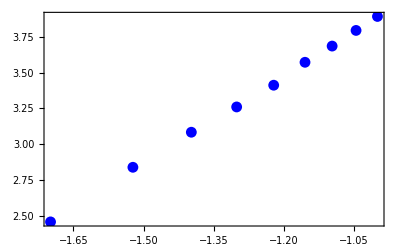

5.91222+2.02909 x

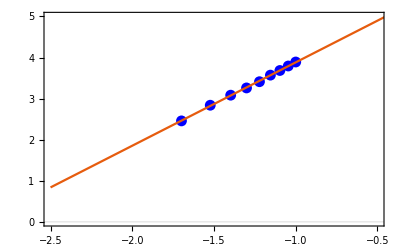

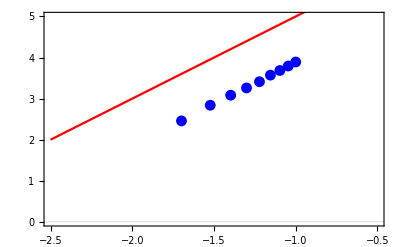

```mathematica
FIG1=ListPlot[Transpose[{Log10[hl],Log10[Fl]}],PlotStyle->Blue,PlotTheme->"Scientific",LabelStyle->Large]
mp=Transpose[{Log10[hl],Log10[Fl]}];
mpf=Fit[mp,{1,x},x]
FIG2=Plot[mpf,{x,-2.5,0},PlotTheme->"Scientific",LabelStyle->Large];
FIG3=Plot[7+2.0*x,{x,-2.5,0},PlotStyle->Red];
Show[{FIG1,FIG2},PlotRange->{{-2.5,-0.5},{0,5}}]
Show[{FIG1,FIG3},PlotRange->{{-2.5,-0.5},{0,5}}]
```

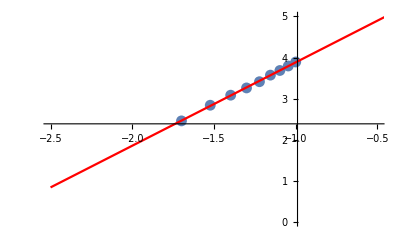

```mathematica
Show[{FIG1,FIG2},PlotRange->{{-2.5,-0.5},{0,5}}]
```

```mathematica
Export["/Users/farzanberoz/Desktop/biophysics/biofilms/1d-film/analysis/plots/sc-scaling-l1.jpg",Show[{FIG1,FIG2},PlotRange->{{-2.5,-0.5},{0,5}}]]
```

/Users/farzanberoz/Desktop/biophysics/biofilms/1d-film/analysis/plots/sc-scaling-l1.jpg